```mathematica
GGrd=ResourceFunction["GeneralizedGridGraph"]
HexaGrid=ResourceFunction["HexagonalGridGraph"]
```

```mathematica
ChordlessCycles[graph_,lngth_]:=Select[FindCycle[graph,{lngth},All],IsomorphicGraphQ[Subgraph[graph,#],CycleGraph[Length[#]]]&]
```

```mathematica
GetEdges[graph_,length_]:=DeleteDuplicates[Sort/@#]&@Flatten[ParallelMap[Subsets[DeleteDuplicates@#,{2}]&@Flatten[({#[[1]],#[[2]]})&/@#]&,ChordlessCycles[graph,length]],1]
SplitEdges[graph_,lengths_]:=DeleteDuplicates[Sort/@#]&/@GatherBy[Flatten[GetEdges[graph,#]&/@lengths,1],GraphDistance[graph,#[[1]],#[[2]]]&]
```

## Testing

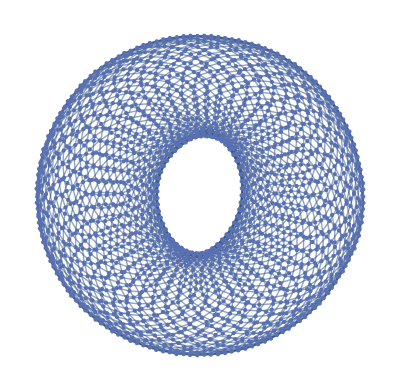

```mathematica
gg=GGrd[{50->"Circular",50->"Circular"}]
```

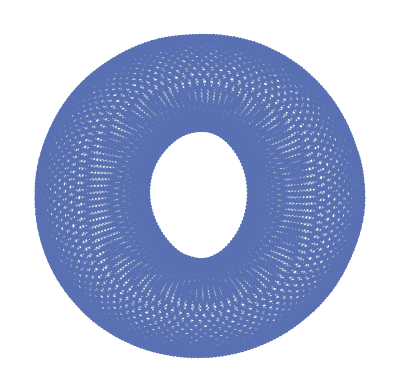

```mathematica
gg2=GGrd[{100->"Circular",100->"Circular"}]
```

```mathematica
AbsoluteTiming[ChordlessCycles[gg,4];]
AbsoluteTiming[ChordlessCycles[gg2,4];]
```

{2.78374,Null}

{36.2,Null}

```mathematica
AbsoluteTiming[splt=SplitEdges[gg,{4}];]
```

{4.31754,Null}

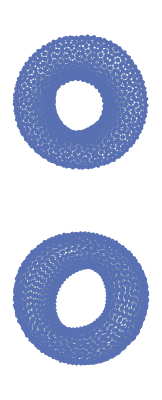
{-Graphics-,-Graphics-}

```mathematica
Graph/@splt
```

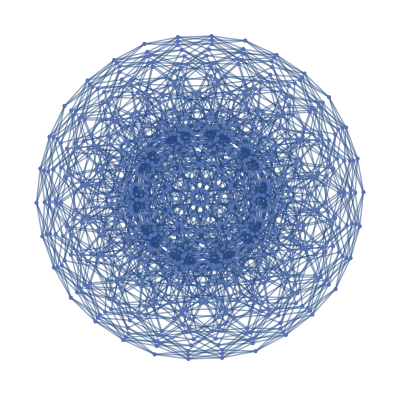

```mathematica
gg3d=GGrd[{10->"Circular",10->"Circular",10->"Circular"}]
```

```mathematica
AbsoluteTiming[splt3d=SplitEdges[gg3d,{4,6}];]
```

{14.9281,Null}

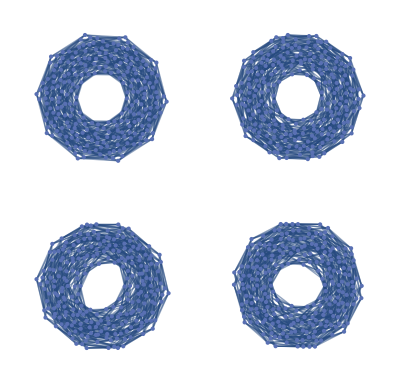
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphPlot[Graph[#]]&/@splt3d
```

```mathematica
AbsoluteTiming[splt3d2=SplitEdges[gg3d,{6}];]
```

{11.7467,Null}

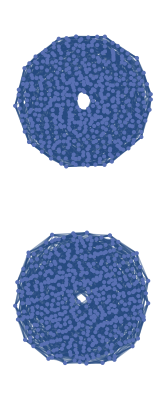
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphPlot[Graph[#]]&/@splt3d2
```

## 2D Squares

```mathematica
AbsoluteTiming[tmp=SplitEdges[GGrd[{50->"Circular",50->"Circular"}],{4}];]
```

{4.29788,Null}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","50x50","1.el"}],tmp[[1]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","50x50","2.el"}],tmp[[2]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\50x50\1.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\50x50\2.el

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","50x50","dists.csv"}],N@Norm[Min[#,50-#]&/@Abs[QuotientRemainder[1,50]-QuotientRemainder[#,50]]]&/@VertexList[GGrd[{50->"Circular",50->"Circular"}]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\graphs\square\50x50\dists.csv

```mathematica
AbsoluteTiming[tmp=SplitEdges[GGrd[{100->"Circular",100->"Circular"}],{4}];]
```

{68.8691,Null}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","100x100","1.el"}],tmp[[1]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","100x100","2.el"}],tmp[[2]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\100x100\1.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\100x100\2.el

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","100x100","dists.csv"}],N@Norm[Min[#,100-#]&/@Abs[QuotientRemainder[1,100]-QuotientRemainder[#,100]]]&/@VertexList[GGrd[{100->"Circular",100->"Circular"}]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\graphs\square\100x100\dists.csv

```mathematica
AbsoluteTiming[tmp=SplitEdges[GGrd[{200->"Circular",200->"Circular"}],{4}];]
```

{2425.79,Null}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","200x200","1.el"}],tmp[[1]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","200x200","2.el"}],tmp[[2]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\200x200\1.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\200x200\2.el

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","200x200","dists.csv"}],N@Norm[Min[#,200-#]&/@Abs[QuotientRemainder[1,200]-QuotientRemainder[#,200]]]&/@VertexList[GGrd[{200->"Circular",200->"Circular"}]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\graphs\square\200x200\dists.csv

## 3D Squares

```mathematica
AbsoluteTiming[tmp=SplitEdges[GGrd[{10->"Circular",10->"Circular",10->"Circular"}],{4,6}];]
```

{14.5265,Null}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","10x10x10","1.el"}],tmp[[1]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","10x10x10","2.el"}],tmp[[2]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","10x10x10","3.el"}],tmp[[3]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\10x10x10\1.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\10x10x10\2.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\10x10x10\3.el

```mathematica
AbsoluteTiming[tmp=SplitEdges[GGrd[{20->"Circular",20->"Circular",20->"Circular"}],{4,6}];]
```

{355.824,Null}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","20x20x20","1.el"}],tmp[[1]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","20x20x20","2.el"}],tmp[[2]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","20x20x20","3.el"}],tmp[[3]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\20x20x20\1.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\20x20x20\2.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\20x20x20\3.el

```mathematica
AbsoluteTiming[tmp=SplitEdges[GGrd[{30->"Circular",30->"Circular",30->"Circular"}],{4,6}];]
```

{8323.99,Null}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","40x40x40","1.el"}],tmp[[1]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","40x40x40","2.el"}],tmp[[2]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","square","40x40x40","3.el"}],tmp[[3]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\40x40x40\1.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\40x40x40\2.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\square\40x40x40\3.el

## 2D Hexagons

```mathematica
√(N@VertexCount[HexaGrid[{35,35}]])
```

50.892

```mathematica
VertexCount[HexaGrid[{35,35}]]
```

2590

```mathematica
AbsoluteTiming[tmp=SplitEdges[HexaGrid[{35,35}],{6}];]
```

{6.27736,Null}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","hex","35x35","1.el"}],tmp[[1]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","hex","35x35","2.el"}],tmp[[2]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","hex","35x35","3.el"}],tmp[[3]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\35x35\1.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\35x35\2.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\35x35\3.el

```mathematica
√(N@VertexCount[HexaGrid[{70,70}]])
```

100.399

```mathematica
VertexCount[HexaGrid[{70,70}]]
```

10080

```mathematica
AbsoluteTiming[tmp=SplitEdges[HexaGrid[{70,70}],{6}];]
```

{104.591,Null}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","hex","70x70","1.el"}],tmp[[1]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","hex","70x70","2.el"}],tmp[[2]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","hex","70x70","3.el"}],tmp[[3]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\70x70\1.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\70x70\2.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\70x70\3.el

```mathematica
√(N@VertexCount[HexaGrid[{140,140}]])
```

199.399

```mathematica
VertexCount[HexaGrid[{140,140}]]
```

39760

```mathematica
AbsoluteTiming[tmp=SplitEdges[HexaGrid[{140,140}],{6}];]
```

{3376.82,Null}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"graphs","hex","140x140","1.el"}],tmp[[1]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","hex","140x140","2.el"}],tmp[[2]],"CSV"]
Export[FileNameJoin[{NotebookDirectory[],"graphs","hex","140x140","3.el"}],tmp[[3]],"CSV"]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\140x140\1.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\140x140\2.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\140x140\3.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\140x140\1.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\140x140\2.el

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\graphs\hex\140x140\3.el

```mathematica
g=Graph[Flatten[{Import@FileNameJoin[{NotebookDirectory[],"graphs","hex","35x35","1.el"}],Import@FileNameJoin[{NotebookDirectory[],"graphs","hex","35x35","2.el"}],Import@FileNameJoin[{NotebookDirectory[],"graphs","hex","35x35","3.el"}]},1]];
```

```mathematica
VertexCount[g]
```

2590

```mathematica
EdgeCount[SimpleGraph@g]
```

14839

```mathematica
DeleteDuplicates@VertexDegree[SimpleGraph@g]
```

{5,9,12}

```mathematica
Counts[VertexDegree[g]]
```

<|5→142,9→136,12→2312|>